```mathematica
image=ColorConvert[Import["http://cs629400.vk.me/v629400099/39bc2/Md48G41EPA8.jpg"],"Grayscale"]
```

-Graphics-

```mathematica
size=ImageDimensions[image];
imageXY[{y_,x_}]:={x,size⟦2⟧+1-y};
minRegionArea=17;
```

```mathematica
edge1=EdgeDetect[image,4];
```

```mathematica
image2=Binarize[image,0.26];
```

```mathematica
components=MorphologicalComponents[image2,0,CornerNeighbors-> False];
count=ComponentMeasurements[components,"Count"];
```

```mathematica
areas=Union[Last/@count];
```

```mathematica
regionNames=First/@Select[count,Last[#]>minRegionArea&];
```

```mathematica
positions=Table[Position[components ImageData[MorphologicalPerimeter[image2,CornerNeighbors-> True],"Bit"],name],{name,regionNames}];
```

```mathematica
boxSides[pt_]:=Partition[{pt+{-1/2,-1/2},pt+{1/2,-1/2},pt+{1/2,1/2},pt+{-1/2,1/2}},2,1,1];
```

```mathematica
signarure[path_]:=Positive@Total[Det/@Partition[path,2,1,1]]
```

```mathematica
contour[pts_]:=Module[{vectors=Join@@(boxSides/@pts),
vertices,edges,
graph,tours},
vertices=Union[First/@vectors];
edges=vectors/.Thread[vertices->Range@Length@vertices];
graph=Graph[DirectedEdge@@@Complement[edges,Intersection[edges,Reverse/@edges]]];
tours=(First/@First@FindPostmanTour@Subgraph[graph,#])&/@ConnectedComponents@graph;
vertices⟦First@Select[tours,signarure[vertices⟦#⟧]&]⟧]
```

```mathematica
perimeters=ParallelMap[contour,positions];//AbsoluteTiming
```

{275.15,Null}

```mathematica
boundaries=Map[imageXY,perimeters,{2}];
```

```mathematica
colors=Join@@Table[ColorData[n,"ColorList"],{n,1,60}];
Graphics[Table[{colors⟦n⟧,Polygon[boundaries⟦n⟧]},{n,Length[boundaries]}],ImageSize->size]
```

-Graphics-

```mathematica
n=13;
linepts = contour[positions⟦n⟧];
```

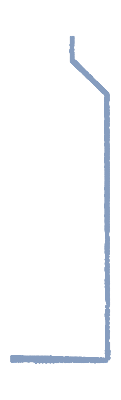
{0.772,-Graphics-}

```mathematica
Ω=DiscretizeRegion[Polygon@linepts, MeshQualityGoal->0.9,MaxCellMeasure->5, AccuracyGoal->0.7]//Timing
```

```mathematica
(*Ω//Last*)
```

InterpolatingFunction[{{0.5, 208.5}, {24.5, 707.5}}, <>]

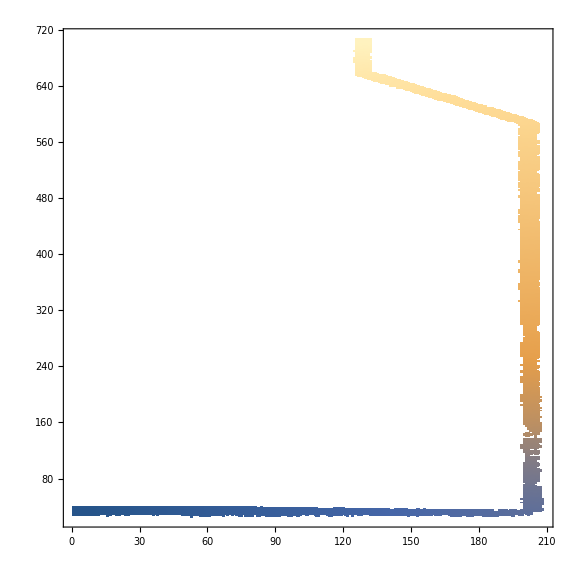

```mathematica
sol00=NDSolveValue[{∇_{x,y}^2 u[x,y]==NeumannValue[0,True],DirichletCondition[u[x,y]==0,x≤ 10],DirichletCondition[u[x,y]==10,y==700]},u,{x,y}∈(Ω//Last)]
DensityPlot[sol00[x,y],{x,y}∈(Ω//Last),ImageSize->Large,PlotRange->Full]
```

```mathematica
Plot3D[sol00[x,y],{x,y}∈(Ω//Last),ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

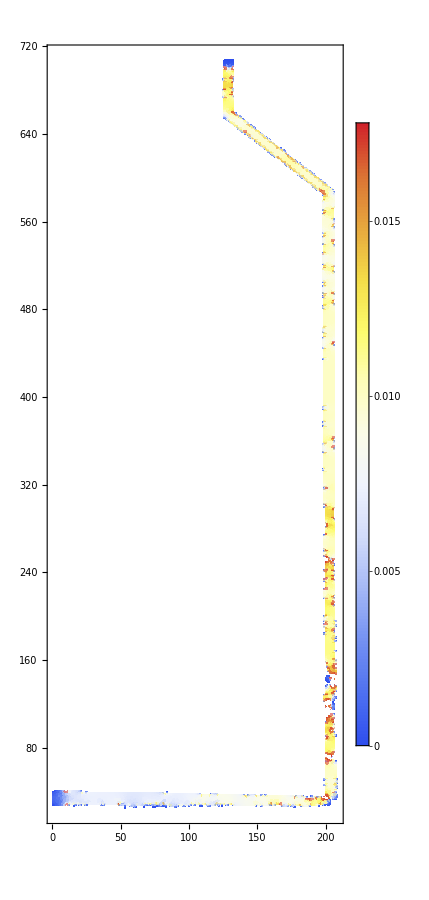

```mathematica
uf=Grad[sol00[x,y],{x,y}];
DensityPlot[Sqrt[uf[[1]]^2+uf[[2]]^2],{x,y}∈(Ω//Last),PlotLegends->Automatic,ColorFunction->"TemperatureMap",ImageSize->Medium,AspectRatio->Automatic]
```

```mathematica
Plot3D[Sqrt[uf[[1]]^2+uf[[2]]^2],{x,y}∈(Ω//Last)]
```

-Graphics3D-

```mathematica
sol01=NDSolveValue[{∇_{x,y}^2 u[x,y]==NeumannValue[0.,y==708],DirichletCondition[u[x,y]==0.,x≥0]},u,{x,y}∈(Ω//Last)]
Plot3D[sol01[x,y],{x,y}∈(Ω//Last)]
```

NDSolveValue::bcnop: No places were found on the boundary where Position was True, so NDSolve`FEM`BoundaryCondition[{Neumann,{1,1},{CompiledFunction[{10,10.3,5568},{_Real,_Real},{{3,0,0},{3,0,1},{3,2,0}},{{{{0.}},{3,2,0}}},{0,0,2,0,1},{{1}},Function[{x,y},{{0.}},Listable],Evaluate]}},Position,{2,{{}}},NeumannValue[0.,y==708]] will effectively be ignored.

InterpolatingFunction[{{0.5, 190.5}, {45.5, 707.5}}, <>]

-Graphics3D-

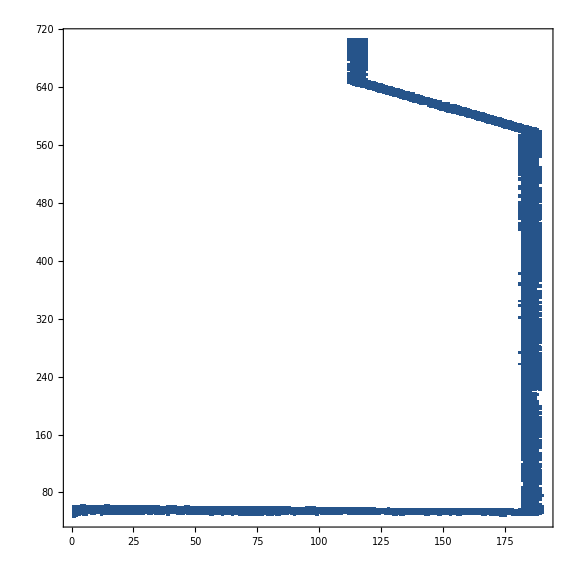

```mathematica
DensityPlot[sol01[x,y],{x,y}∈(Ω//Last),ImageSize->Large]
```

```mathematica
pts={{0,0},{0,2},{5,2},{8,5},{10,5},{10,3},{8,3},{5,0}}
pts=Rectangle[{0,0},{5,3}]
```

{{0,0},{0,2},{5,2},{8,5},{10,5},{10,3},{8,3},{5,0}}

Rectangle[{0,0},{5,3}]

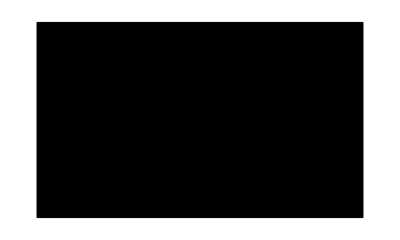

```mathematica
Graphics[pts]
```

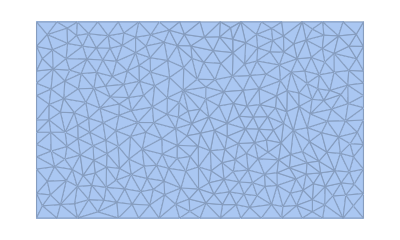

```mathematica
Ω=DiscretizeRegion[pts]
```

NDSolveValue::bcnop: No places were found on the boundary where Position was True, so NDSolve`FEM`BoundaryCondition[{Neumann,{1,1},{CompiledFunction[{10,10.3,5568},{_Real,_Real},{{3,0,0},{3,0,1},{3,2,0}},{{{{0.}},{3,2,0}}},{0,0,2,0,1},{{1}},Function[{x,y},{{0.}},Listable],Evaluate]}},Position,{2,{{}}},NeumannValue[0.,x==3]] will effectively be ignored.

InterpolatingFunction[{{0., 5.}, {0., 3.}}, <>]

-Graphics3D-

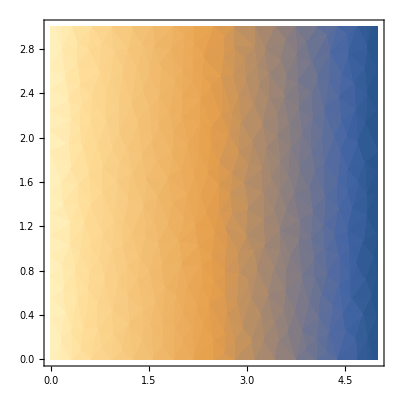

```mathematica
sol01=NDSolveValue[{∇_{x,y}^2 u[x,y]==NeumannValue[1.,x==5]+NeumannValue[0.,y==0]+NeumannValue[0.,x==3],
DirichletCondition[u[x,y]==0.,x==0]},
u,{x,y}∈(Ω)]
Plot3D[sol01[x,y],{x,y}∈(Ω)]
DensityPlot[sol01[x,y],{x,y}∈(Ω)]
```